## Config

```mathematica
(* Provide the location of the randgeom executable *)
(* On windows change randgeom to randgeom.exe *)
programlocation = "/home/mgv29/Desktop/randgeom"
```

/home/mgv29/Desktop/randgeom

```mathematica
""/home/mgv29/Desktop/randgeom
```

/(Desktop home mgv29 randgeom)

```mathematica
(* Test the program. If it return False, check the programlocation provided. If it still does not work, first test randgeom from the console. *)
FileExistsQ[programlocation]&&ListQ[RunThrough["'"<>programlocation<>"'",""]]
```

True

## Useful functions

```mathematica
(* the following just runs randgeom with the specified parameters and parses the output as Mathematica code *)
generateMaps[type_,size_,number_]:=RunThrough["'"<>programlocation<>"' -t"<>type<>" -s"<>ToString[size]<>" -n"<>ToString[number], ""];
generateMap[type_,size_]:=First@generateMaps[type,size,1];
```

```mathematica
(* given a permutation p of {1,2,...,n}, cycles[p] gives the partition of {1,2,...,n} into cycles *)
cycles[p_]:=PermutationCycles[p,Identity];
(* given a list plist of permutations, orbits[plist] gives the partition of {1,2,...,n} into orbits under the permutations *)
orbits[plist_]:=GroupOrbits@PermutationGroup[PermutationCycles/@plist]
```

```mathematica
(* edges, vertices and faces correspond to cycles of halfedge-permutations *)
edgecycles[map_]:=cycles[map[[All,3]]];
facecycles[map_]:=cycles[map[[All,1]]];
vertexcycles[map_]:=cycles[map[[map[[All,3]],1]]];
(* We may assign id's to the vertices of map according to their position in vertexcycles[map] *)
halfedgeToVertexId[map_]:=Dispatch[Join@@MapIndexed[#1->#2[[1]]&,vertexcycles[map],{2}]];
halfedgeToFaceId[map_]:=Dispatch[Join@@MapIndexed[#1->#2[[1]]&,facecycles[map],{2}]];
```

```mathematica
(* functions to construct a Mathematica Graph object *)
uniqueEdges[map_]:=Union[Sort/@(edgecycles[map]/.halfedgeToVertexId[map])];
uniqueDualEdges[map_]:=Union[Sort/@(edgecycles[map]/.halfedgeToFaceId[map])];
mapGraph[map_]:=With[{edges=uniqueEdges[map]},Graph[Union@@edges,#[[1]]<->#[[2]]&/@edges,GraphLayout->None]];
mapDualGraph[map_]:=With[{edges=uniqueDualEdges[map]},Graph[Union@@edges,#[[1]]<->#[[2]]&/@edges,GraphLayout->None]];
```

## Plotting

```mathematica
(* the following is a bit of a hack to extract coordinates from GraphPlot3D's embedding of a graph *)
get3DGraphEmbedding[edg_,method_]:=(VertexCoordinateRules /. Cases[GraphPlot3D[#[[1]]->#[[2]]&/@edg,Method->method], _Rule, Infinity])[[Ordering@DeleteDuplicates[Join@@(List@@@edg)]]];
```

```mathematica
(* one can play with the options here to adapt the embedding *)
coordinates[map_]:=get3DGraphEmbedding[uniqueEdges[map],{"SpringElectricalEmbedding","InferentialDistance"->Automatic,"RepulsiveForcePower"->-2.4}];
```

```mathematica
(* assign colors to faces according to closeness centrality *)
colorFunction[x_]:=ColorData["Rainbow"][Round[Max[Min[0.55-0.15x,1],0],1/40]];
centralityColors[map_]:=colorFunction/@Standardize@ClosenessCentrality[mapDualGraph[map]];
```

```mathematica
plotMap3D[map_,coor_]:=Graphics3D[{EdgeForm[None],{FaceForm[#[[1]]],Polygon[coor[[#[[2,;;3]]]]],If[Length[#[[2]]]==4,Polygon[coor[[#[[2,{1,3,4}]]]]],{}]}&/@Transpose[{centralityColors[map],facecycles[map]/.halfedgeToVertexId[map]}]},Boxed->False]
```

```mathematica
meth = {"SpringElectricalEmbedding","InferentialDistance"->Automatic,"RepulsiveForcePower"->-2.7}
map1=generateMap["C",500]
```

{SpringElectricalEmbedding,InferentialDistance→Automatic,RepulsiveForcePower→-2.7}

{{15,18,2},{1997,2000,1},{5,8,4},{1988,1985,3},{14,3,6},{1986,1983,5},{12,9,8},{3,14,7},{7,10,10},{9,12,9},{13,16,12},{10,7,11},{22,11,14},{8,5,13},{20,1,16},{11,22,15},{59,62,18},{1,20,17},{41,44,20},{18,15,19},{39,42,22},{16,13,21},{28,37,24},{1976,1973,23},{35,38,26},{37,28,25},{33,36,28},{26,23,27},{31,34,30},{1974,1971,29},{456,29,32},{1960,1957,31},{436,27,34},{29,456,33},{40,25,36},{27,436,35},{23,26,38},{25,40,37},{48,21,40},{38,35,39},{46,19,42},{21,48,41},{53,56,44},{19,46,43},{47,50,46},{44,41,45},{356,45,48},{42,39,47},{54,51,50},{45,356,49},{49,52,52},{51,54,51},{58,43,54},{52,49,53},{57,60,56},{43,58,55},{68,55,58},{56,53,57},{66,17,60},{55,68,59},{63,1998,62},{17,66,61},{1995,61,64},{1985,1988,63},{1983,1986,66},{62,59,65},{172,713,68},{60,57,67},{130,323,70},{713,172,69},{76,73,72},{323,130,71},{71,74,74},{73,76,73},{84,81,76},{74,71,75},{82,79,78},{81,84,77},{77,80,80},{79,82,79},{75,78,82},{80,77,81},{88,321,84},{78,75,83},{87,90,86},{321,88,85},{96,85,88},{86,83,87},{94,91,90},{85,96,89},{89,92,92},{91,94,91},{319,322,94},{92,89,93},{108,269,96},{90,87,95},{102,99,98},{269,108,97},{97,100,100},{99,102,99},{106,103,102},{100,97,101},{101,104,104},{103,106,103},{107,110,106},{104,101,105},{118,105,108},{98,95,107},{114,111,110},{105,118,109},{109,112,112},{111,114,111},{115,246,114},{112,109,113},{243,113,116},{241,244,115},{119,122,118},{110,107,117},{120,117,120},{122,119,119},{123,126,122},{117,120,121},{124,121,124},{126,123,123},{127,210,126},{121,124,125},{207,125,128},{201,204,127},{134,131,130},{72,69,129},{129,132,132},{131,134,131},{166,163,134},{132,129,133},{137,144,136},{163,166,135},{141,135,138},{142,139,137},{138,140,140},{139,142,139},{144,137,142},{140,138,141},{156,161,144},{135,141,143},{147,162,146},{161,156,145},{159,145,148},{152,149,147},{148,150,150},{149,152,149},{153,160,152},{150,148,151},{157,151,154},{155,158,153},{164,154,156},{146,143,155},{160,153,158},{154,164,157},{162,147,160},{151,157,159},{143,146,162},{145,159,161},{133,136,164},{158,155,163},{170,167,166},{136,133,165},{165,168,168},{167,170,167},{199,202,170},{168,165,169},{176,173,172},{70,67,171},{171,174,174},{173,176,173},{177,180,176},{174,171,175},{178,175,178},{180,177,177},{184,181,180},{175,178,179},{179,182,182},{181,184,181},{200,197,184},{182,179,183},{190,191,186},{197,200,185},{189,192,188},{191,190,187},{194,187,190},{188,185,189},{185,188,192},{187,194,191},{195,198,194},{192,189,193},{196,193,196},{198,195,195},{183,186,198},{193,196,197},{290,169,200},{186,183,199},{206,128,202},{169,290,201},{205,208,204},{128,206,203},{218,203,206},{204,201,205},{210,127,208},{203,218,207},{211,230,210},{125,207,209},{227,209,212},{213,216,211},{214,212,214},{216,213,213},{225,228,216},{212,214,215},{219,222,218},{208,205,217},{220,217,220},{222,219,219},{223,226,222},{217,220,221},{224,221,224},{226,223,223},{240,215,226},{221,224,225},{230,211,228},{215,240,227},{234,231,230},{209,227,229},{229,232,232},{231,234,231},{235,238,234},{232,229,233},{236,233,236},{238,235,235},{239,242,238},{233,236,237},{276,237,240},{228,225,239},{248,116,242},{237,276,241},{246,115,244},{116,248,243},{267,270,246},{113,243,245},{249,268,248},{244,241,247},{265,247,250},{262,259,249},{256,253,252},{259,262,251},{251,254,254},{253,256,253},{257,260,256},{254,251,255},{258,255,258},{260,257,257},{250,252,260},{255,258,259},{263,266,262},{252,250,261},{264,261,264},{266,263,263},{268,249,266},{261,264,265},{272,245,268},{247,265,267},{95,98,270},{245,272,269},{273,320,272},{270,267,271},{317,271,274},{275,278,273},{288,274,276},{242,239,275},{282,283,278},{274,288,277},{281,284,280},{283,282,279},{286,279,282},{280,277,281},{277,280,284},{279,286,283},{315,318,286},{284,281,285},{293,296,288},{278,275,287},{294,291,290},{202,199,289},{289,292,292},{291,294,291},{300,287,294},{292,289,293},{297,304,296},{287,300,295},{301,295,298},{299,302,297},{306,298,300},{296,293,299},{304,297,302},{298,306,301},{305,308,304},{295,301,303},{310,303,306},{302,299,305},{313,316,308},{303,310,307},{311,314,310},{308,305,309},{312,309,312},{314,311,311},{330,307,314},{309,312,313},{326,285,316},{307,330,315},{320,273,318},{285,326,317},{324,93,320},{271,317,319},{83,86,322},{93,324,321},{69,72,324},{322,319,323},{327,714,326},{318,315,325},{711,325,328},{709,712,327},{334,331,330},{316,313,329},{329,332,332},{331,334,331},{335,338,334},{332,329,333},{336,333,336},{338,335,335},{339,342,338},{333,336,337},{340,337,340},{342,339,339},{343,710,342},{337,340,341},{707,341,344},{352,693,343},{350,691,346},{693,352,345},{361,364,348},{691,350,347},{359,362,350},{348,345,349},{353,360,352},{346,344,351},{357,351,354},{355,358,353},{404,354,356},{50,47,355},{360,353,358},{354,404,357},{402,349,360},{351,357,359},{366,347,362},{349,402,361},{549,552,364},{347,366,363},{386,383,366},{364,361,365},{384,381,368},{383,386,367},{382,379,370},{381,384,369},{376,373,372},{379,382,371},{371,374,374},{373,376,373},{377,380,376},{374,371,375},{378,375,378},{380,377,377},{369,372,380},{375,378,379},{367,370,382},{372,369,381},{365,368,384},{370,367,383},{387,550,386},{368,365,385},{547,385,388},{392,397,387},{391,394,390},{397,392,389},{400,389,392},{390,388,391},{395,398,394},{389,400,393},{396,393,396},{398,395,395},{388,390,398},{393,396,397},{409,412,400},{394,391,399},{407,410,402},{362,359,401},{405,408,404},{358,355,403},{406,403,406},{408,405,405},{434,401,408},{403,406,407},{432,399,410},{401,434,409},{416,413,412},{399,432,411},{411,414,414},{413,416,413},{424,545,416},{414,411,415},{422,419,418},{545,424,417},{417,420,420},{419,422,419},{543,546,422},{420,417,421},{425,544,424},{418,415,423},{541,423,426},{430,427,425},{426,428,428},{427,430,427},{539,542,430},{428,426,429},{537,540,432},{412,409,431},{479,482,434},{410,407,433},{440,437,436},{36,33,435},{435,438,438},{437,440,437},{441,472,440},{438,435,439},{469,439,442},{446,451,441},{449,452,444},{451,446,443},{450,447,446},{444,442,445},{445,448,448},{447,450,447},{454,443,450},{448,445,449},{442,444,452},{443,454,451},{459,462,454},{452,449,453},{460,457,456},{34,31,455},{455,458,458},{457,460,457},{474,453,460},{458,455,459},{466,467,462},{453,474,461},{465,468,464},{467,466,463},{470,463,466},{464,461,465},{461,464,468},{463,470,467},{472,441,470},{468,465,469},{477,480,472},{439,469,471},{475,478,474},{462,459,473},{498,473,476},{1958,1955,475},{496,471,478},{473,498,477},{484,433,480},{471,496,479},{527,530,482},{433,484,481},{485,528,484},{482,479,483},{525,483,486},{487,526,485},{523,486,488},{489,492,487},{490,488,490},{492,489,489},{493,524,492},{488,490,491},{521,491,494},{515,518,493},{505,508,496},{480,477,495},{499,502,498},{478,475,497},{500,497,500},{502,499,499},{503,506,502},{497,500,501},{504,501,504},{506,503,503},{514,495,506},{501,504,505},{512,509,508},{495,514,507},{507,510,510},{509,512,509},{513,516,512},{510,507,511},{778,511,514},{508,505,513},{520,494,516},{511,778,515},{519,522,518},{494,520,517},{736,517,520},{518,515,519},{524,493,522},{517,736,521},{526,487,524},{491,521,523},{528,485,526},{486,523,525},{532,481,528},{483,525,527},{535,538,530},{481,532,529},{533,536,532},{530,527,531},{534,531,534},{536,533,533},{726,529,536},{531,534,535},{594,431,538},{529,726,537},{584,429,540},{431,594,539},{544,425,542},{429,584,541},{548,421,544},{423,541,543},{415,418,546},{421,548,545},{550,387,548},{546,543,547},{562,363,550},{385,547,549},{553,636,552},{363,562,551},{633,551,554},{555,634,553},{631,554,556},{557,576,555},{573,556,558},{559,570,557},{567,558,560},{565,568,559},{563,566,562},{552,549,561},{564,561,564},{566,563,563},{572,560,566},{561,564,565},{570,559,568},{560,572,567},{571,574,570},{558,567,569},{578,569,572},{568,565,571},{576,557,574},{569,578,573},{577,580,576},{556,573,575},{582,575,578},{574,571,577},{625,628,580},{575,582,579},{623,626,582},{580,577,581},{585,624,584},{542,539,583},{621,583,586},{587,622,585},{619,586,588},{592,617,587},{599,602,590},{617,592,589},{593,596,592},{590,588,591},{722,591,594},{540,537,593},{600,597,596},{591,722,595},{595,598,598},{597,600,597},{604,589,600},{598,595,599},{607,610,602},{589,604,601},{608,605,604},{602,599,603},{603,606,606},{605,608,605},{614,601,608},{606,603,607},{611,618,610},{601,614,609},{615,609,612},{613,616,611},{620,612,614},{610,607,613},{618,611,616},{612,620,615},{588,590,618},{609,615,617},{622,587,620},{616,613,619},{624,585,622},{586,619,621},{696,581,624},{583,621,623},{674,579,626},{581,696,625},{629,632,628},{579,674,627},{630,627,630},{632,629,629},{634,555,632},{627,630,631},{636,553,634},{554,631,633},{640,689,636},{551,633,635},{675,678,638},{689,640,637},{660,669,640},{638,635,639},{652,655,642},{669,660,641},{645,648,644},{655,652,643},{646,643,646},{648,645,645},{649,656,648},{643,646,647},{653,647,650},{651,654,649},{658,650,652},{644,641,651},{656,649,654},{650,658,653},{641,644,656},{647,653,655},{659,662,658},{654,651,657},{672,657,660},{642,639,659},{663,666,662},{657,672,661},{664,661,664},{666,663,663},{670,667,666},{661,664,665},{665,668,668},{667,670,667},{639,642,670},{668,665,669},{673,676,672},{662,659,671},{694,671,674},{628,625,673},{682,637,676},{671,694,675},{679,690,678},{637,682,677},{687,677,680},{681,684,679},{692,680,682},{678,675,681},{688,685,684},{680,692,683},{683,686,686},{685,688,685},{690,679,688},{686,683,687},{635,638,690},{677,687,689},{345,348,692},{684,681,691},{344,346,694},{676,673,693},{704,701,696},{626,623,695},{699,702,698},{701,704,697},{700,697,700},{702,699,699},{695,698,702},{697,700,701},{708,705,704},{698,695,703},{703,706,706},{705,708,705},{710,343,708},{706,703,707},{716,328,710},{341,707,709},{714,327,712},{328,716,711},{67,70,714},{325,711,713},{717,1984,716},{712,709,715},{1981,715,718},{719,1978,717},{1975,718,720},{1973,1976,719},{723,750,722},{596,593,721},{747,721,724},{725,728,723},{734,724,726},{538,535,725},{732,729,728},{724,734,727},{727,730,730},{729,732,729},{745,748,732},{730,727,731},{735,738,734},{728,725,733},{756,733,736},{522,519,735},{746,743,738},{733,756,737},{744,741,740},{743,746,739},{739,742,742},{741,744,741},{737,740,744},{742,739,743},{754,731,746},{740,737,745},{750,723,748},{731,754,747},{751,1970,750},{721,747,749},{1967,749,752},{1965,1968,751},{755,758,754},{748,745,753},{768,753,756},{738,735,755},{759,806,758},{753,768,757},{803,757,760},{761,800,759},{797,760,762},{763,766,761},{764,762,764},{766,763,763},{795,798,766},{762,764,765},{769,796,768},{758,755,767},{793,767,770},{771,786,769},{783,770,772},{773,776,771},{774,772,774},{776,773,773},{777,780,776},{772,774,775},{782,775,778},{516,513,777},{781,784,780},{775,782,779},{818,779,782},{780,777,781},{786,771,784},{779,818,783},{790,791,786},{770,783,785},{789,792,788},{791,790,787},{794,787,790},{788,785,789},{785,788,792},{787,794,791},{796,769,794},{792,789,793},{808,765,796},{767,793,795},{800,761,798},{765,808,797},{804,801,800},{760,797,799},{799,802,802},{801,804,801},{806,759,804},{802,799,803},{1895,1898,806},{757,803,805},{812,809,808},{798,795,807},{807,810,810},{809,812,809},{813,816,812},{810,807,811},{814,811,814},{816,813,813},{1541,1544,816},{811,814,815},{822,819,818},{784,781,817},{817,820,820},{819,822,819},{823,826,822},{820,817,821},{824,821,824},{826,823,823},{836,1539,826},{821,824,825},{829,980,828},{1539,836,827},{977,827,830},{831,978,829},{975,830,832},{833,860,831},{857,832,834},{839,842,833},{837,840,836},{828,825,835},{1564,835,838},{1892,1889,837},{932,834,840},{835,1564,839},{846,855,842},{834,932,841},{853,856,844},{855,846,843},{850,851,846},{844,841,845},{849,852,848},{851,850,847},{854,847,850},{848,845,849},{845,848,852},{847,854,851},{858,843,854},{852,849,853},{841,844,856},{843,858,855},{860,833,858},{856,853,857},{928,973,860},{832,857,859},{863,866,862},{973,928,861},{864,861,864},{866,863,863},{872,951,866},{861,864,865},{869,948,868},{951,872,867},{945,867,870},{875,878,869},{876,873,872},{868,865,871},{871,874,874},{873,876,873},{890,870,876},{874,871,875},{879,946,878},{870,890,877},{943,877,880},{884,885,879},{883,886,882},{885,884,881},{888,881,884},{882,880,883},{880,882,886},{881,888,885},{937,940,888},{886,883,887},{891,926,890},{878,875,889},{923,889,892},{924,921,891},{898,919,894},{921,924,893},{917,920,896},{919,898,895},{899,918,898},{896,893,897},{915,897,900},{912,909,899},{910,907,902},{909,912,901},{905,908,904},{907,910,903},{906,903,906},{908,905,905},{901,904,908},{903,906,907},{900,902,910},{904,901,909},{916,913,912},{902,900,911},{911,914,914},{913,916,913},{918,899,916},{914,911,915},{922,895,918},{897,915,917},{893,896,920},{895,922,919},{892,894,922},{920,917,921},{926,891,924},{894,892,923},{935,938,926},{889,923,925},{929,936,928},{862,859,927},{933,927,930},{931,934,929},{1246,930,932},{842,839,931},{936,929,934},{930,1246,933},{960,925,936},{927,933,935},{954,887,938},{925,960,937},{944,941,940},{887,954,939},{939,942,942},{941,944,941},{946,879,944},{942,939,943},{948,869,946},{877,943,945},{952,949,948},{867,945,947},{947,950,950},{949,952,949},{865,868,952},{950,947,951},{955,958,954},{940,937,953},{956,953,956},{958,955,955},{971,974,958},{953,956,957},{972,969,960},{938,935,959},{963,966,962},{969,972,961},{964,961,964},{966,963,963},{970,967,966},{961,964,965},{965,968,968},{967,970,967},{959,962,970},{968,965,969},{976,957,972},{962,959,971},{859,862,974},{957,976,973},{978,831,976},{974,971,975},{980,829,978},{830,975,977},{1054,1513,980},{827,977,979},{986,983,982},{1513,1054,981},{981,984,984},{983,986,983},{1012,1511,986},{984,981,985},{989,1512,988},{1511,1012,987},{1509,987,990},{998,1027,989},{993,996,992},{1027,998,991},{994,991,994},{996,993,993},{1025,1028,996},{991,994,995},{1002,999,998},{992,990,997},{997,1000,1000},{999,1002,999},{1006,1007,1002},{1000,997,1001},{1005,1008,1004},{1007,1006,1003},{1010,1003,1006},{1004,1001,1005},{1001,1004,1008},{1003,1010,1007},{1023,1026,1010},{1008,1005,1009},{1024,1021,1012},{988,985,1011},{1015,1018,1014},{1021,1024,1013},{1016,1013,1016},{1018,1015,1015},{1019,1022,1018},{1013,1016,1017},{1020,1017,1020},{1022,1019,1019},{1011,1014,1022},{1017,1020,1021},{1032,1009,1024},{1014,1011,1023},{1030,995,1026},{1009,1032,1025},{990,992,1028},{995,1030,1027},{1031,1034,1030},{1028,1025,1029},{1048,1029,1032},{1026,1023,1031},{1035,1510,1034},{1029,1048,1033},{1507,1033,1036},{1037,1044,1035},{1041,1036,1038},{1042,1039,1037},{1038,1040,1040},{1039,1042,1039},{1044,1037,1042},{1040,1038,1041},{1045,1508,1044},{1036,1041,1043},{1505,1043,1046},{1067,1070,1045},{1052,1049,1048},{1034,1031,1047},{1047,1050,1050},{1049,1052,1049},{1065,1068,1052},{1050,1047,1051},{1055,1066,1054},{982,979,1053},{1063,1053,1056},{1057,1060,1055},{1058,1056,1058},{1060,1057,1057},{1061,1064,1060},{1056,1058,1059},{1062,1059,1062},{1064,1061,1061},{1066,1055,1064},{1059,1062,1063},{1086,1051,1066},{1053,1063,1065},{1084,1046,1068},{1051,1086,1067},{1082,1135,1070},{1046,1084,1069},{1073,1112,1072},{1135,1082,1071},{1109,1071,1074},{1075,1110,1073},{1107,1074,1076},{1077,1108,1075},{1105,1076,1078},{1079,1094,1077},{1091,1078,1080},{1089,1092,1079},{1087,1090,1082},{1072,1069,1081},{1085,1088,1084},{1070,1067,1083},{1244,1083,1086},{1068,1065,1085},{1142,1081,1088},{1083,1244,1087},{1096,1080,1090},{1081,1142,1089},{1094,1079,1092},{1080,1096,1091},{1095,1098,1094},{1078,1091,1093},{1104,1093,1096},{1092,1089,1095},{1102,1099,1098},{1093,1104,1097},{1097,1100,1100},{1099,1102,1099},{1103,1106,1102},{1100,1097,1101},{1138,1101,1104},{1098,1095,1103},{1108,1077,1106},{1101,1138,1105},{1110,1075,1108},{1076,1105,1107},{1112,1073,1110},{1074,1107,1109},{1116,1117,1112},{1071,1109,1111},{1115,1118,1114},{1117,1116,1113},{1120,1113,1116},{1114,1111,1115},{1111,1114,1118},{1113,1120,1117},{1121,1128,1120},{1118,1115,1119},{1125,1119,1122},{1123,1126,1121},{1124,1122,1124},{1126,1123,1123},{1128,1121,1126},{1122,1124,1125},{1132,1129,1128},{1119,1125,1127},{1127,1130,1130},{1129,1132,1129},{1136,1133,1132},{1130,1127,1131},{1131,1134,1134},{1133,1136,1133},{1069,1072,1136},{1134,1131,1135},{1139,1434,1138},{1106,1103,1137},{1431,1137,1140},{1429,1432,1139},{1143,1150,1142},{1090,1087,1141},{1147,1141,1144},{1148,1145,1143},{1144,1146,1146},{1145,1148,1145},{1150,1143,1148},{1146,1144,1147},{1151,1370,1150},{1141,1147,1149},{1367,1149,1152},{1214,1365,1151},{1158,1319,1154},{1365,1214,1153},{1317,1320,1156},{1319,1158,1155},{1159,1306,1158},{1156,1153,1157},{1303,1157,1160},{1186,1237,1159},{1184,1203,1162},{1237,1186,1161},{1165,1172,1164},{1203,1184,1163},{1169,1163,1166},{1170,1167,1165},{1166,1168,1168},{1167,1170,1167},{1172,1165,1170},{1168,1166,1169},{1176,1173,1172},{1163,1169,1171},{1171,1174,1174},{1173,1176,1173},{1177,1180,1176},{1174,1171,1175},{1178,1175,1178},{1180,1177,1177},{1181,1200,1180},{1175,1178,1179},{1197,1179,1182},{1187,1190,1181},{1185,1188,1184},{1164,1161,1183},{1208,1183,1186},{1162,1160,1185},{1206,1182,1188},{1183,1208,1187},{1191,1198,1190},{1182,1206,1189},{1195,1189,1192},{1193,1196,1191},{1194,1192,1194},{1196,1193,1193},{1198,1191,1196},{1192,1194,1195},{1200,1181,1198},{1189,1195,1197},{1201,1204,1200},{1179,1197,1199},{1202,1199,1202},{1204,1201,1201},{1161,1164,1204},{1199,1202,1203},{1207,1210,1206},{1190,1187,1205},{1212,1205,1208},{1188,1185,1207},{1235,1238,1210},{1205,1212,1209},{1233,1236,1212},{1210,1207,1211},{1215,1230,1214},{1154,1152,1213},{1227,1213,1216},{1217,1224,1215},{1221,1216,1218},{1222,1219,1217},{1218,1220,1220},{1219,1222,1219},{1224,1217,1222},{1220,1218,1221},{1225,1228,1224},{1216,1221,1223},{1226,1223,1226},{1228,1225,1225},{1230,1215,1228},{1223,1226,1227},{1234,1231,1230},{1213,1227,1229},{1229,1232,1232},{1231,1234,1231},{1242,1211,1234},{1232,1229,1233},{1240,1209,1236},{1211,1242,1235},{1160,1162,1238},{1209,1240,1237},{1297,1300,1240},{1238,1235,1239},{1283,1286,1242},{1236,1233,1241},{1245,1248,1244},{1088,1085,1243},{1280,1243,1246},{934,931,1245},{1249,1284,1248},{1243,1280,1247},{1281,1247,1250},{1262,1271,1249},{1253,1256,1252},{1271,1262,1251},{1254,1251,1254},{1256,1253,1253},{1257,1260,1256},{1251,1254,1255},{1258,1255,1258},{1260,1257,1257},{1265,1268,1260},{1255,1258,1259},{1263,1266,1262},{1252,1250,1261},{1264,1261,1264},{1266,1263,1263},{1270,1259,1266},{1261,1264,1265},{1269,1272,1268},{1259,1270,1267},{1274,1267,1270},{1268,1265,1269},{1250,1252,1272},{1267,1274,1271},{1278,1275,1274},{1272,1269,1273},{1273,1276,1276},{1275,1278,1275},{1279,1282,1278},{1276,1273,1277},{1398,1277,1280},{1248,1245,1279},{1284,1249,1282},{1277,1398,1281},{1384,1241,1284},{1247,1281,1283},{1290,1287,1286},{1241,1384,1285},{1285,1288,1288},{1287,1290,1287},{1291,1294,1290},{1288,1285,1289},{1292,1289,1292},{1294,1291,1291},{1295,1298,1294},{1289,1292,1293},{1296,1293,1296},{1298,1295,1295},{1316,1239,1298},{1293,1296,1297},{1304,1301,1300},{1239,1316,1299},{1299,1302,1302},{1301,1304,1301},{1306,1159,1304},{1302,1299,1303},{1314,1311,1306},{1157,1303,1305},{1309,1312,1308},{1311,1314,1307},{1310,1307,1310},{1312,1309,1309},{1305,1308,1312},{1307,1310,1311},{1315,1318,1314},{1308,1305,1313},{1368,1313,1316},{1300,1297,1315},{1322,1155,1318},{1313,1368,1317},{1153,1156,1320},{1155,1322,1319},{1366,1363,1322},{1320,1317,1321},{1332,1329,1324},{1363,1366,1323},{1330,1327,1326},{1329,1332,1325},{1325,1328,1328},{1327,1330,1327},{1323,1326,1330},{1328,1325,1329},{1342,1361,1332},{1326,1323,1331},{1338,1335,1334},{1361,1342,1333},{1333,1336,1336},{1335,1338,1335},{1339,1358,1338},{1336,1333,1337},{1355,1337,1340},{1341,1344,1339},{1354,1340,1342},{1334,1331,1341},{1345,1352,1344},{1340,1354,1343},{1349,1343,1346},{1347,1350,1345},{1348,1346,1348},{1350,1347,1347},{1352,1345,1350},{1346,1348,1349},{1353,1356,1352},{1343,1349,1351},{1364,1351,1354},{1344,1341,1353},{1358,1339,1356},{1351,1364,1355},{1362,1359,1358},{1337,1355,1357},{1357,1360,1360},{1359,1362,1359},{1331,1334,1362},{1360,1357,1361},{1321,1324,1364},{1356,1353,1363},{1152,1154,1366},{1324,1321,1365},{1370,1151,1368},{1318,1315,1367},{1374,1375,1370},{1149,1367,1369},{1373,1376,1372},{1375,1374,1371},{1378,1371,1374},{1372,1369,1373},{1369,1372,1376},{1371,1378,1375},{1382,1427,1378},{1376,1373,1377},{1421,1424,1380},{1427,1382,1379},{1391,1394,1382},{1380,1377,1381},{1385,1388,1384},{1286,1283,1383},{1386,1383,1386},{1388,1385,1385},{1392,1389,1388},{1383,1386,1387},{1387,1390,1390},{1389,1392,1389},{1396,1381,1392},{1390,1387,1391},{1403,1406,1394},{1381,1396,1393},{1401,1404,1396},{1394,1391,1395},{1399,1402,1398},{1282,1279,1397},{1400,1397,1400},{1402,1399,1399},{1542,1395,1402},{1397,1400,1401},{1408,1393,1404},{1395,1542,1403},{1407,1410,1406},{1393,1408,1405},{1420,1405,1408},{1406,1403,1407},{1418,1415,1410},{1405,1420,1409},{1413,1416,1412},{1415,1418,1411},{1414,1411,1414},{1416,1413,1413},{1409,1412,1416},{1411,1414,1415},{1419,1422,1418},{1412,1409,1417},{1516,1417,1420},{1410,1407,1419},{1426,1379,1422},{1417,1516,1421},{1425,1428,1424},{1379,1426,1423},{1430,1423,1426},{1424,1421,1425},{1377,1380,1428},{1423,1430,1427},{1482,1140,1430},{1428,1425,1429},{1434,1139,1432},{1140,1482,1431},{1442,1503,1434},{1137,1431,1433},{1440,1497,1436},{1503,1442,1435},{1459,1462,1438},{1497,1440,1437},{1441,1444,1440},{1438,1435,1439},{1450,1439,1442},{1436,1433,1441},{1448,1445,1444},{1439,1450,1443},{1443,1446,1446},{1445,1448,1445},{1449,1452,1448},{1446,1443,1447},{1480,1447,1450},{1444,1441,1449},{1456,1457,1452},{1447,1480,1451},{1455,1458,1454},{1457,1456,1453},{1460,1453,1456},{1454,1451,1455},{1451,1454,1458},{1453,1460,1457},{1476,1437,1460},{1458,1455,1459},{1463,1470,1462},{1437,1476,1461},{1467,1461,1464},{1465,1468,1463},{1466,1464,1466},{1468,1465,1465},{1470,1463,1468},{1464,1466,1467},{1474,1471,1470},{1461,1467,1469},{1469,1472,1472},{1471,1474,1471},{1495,1498,1474},{1472,1469,1473},{1477,1492,1476},{1462,1459,1475},{1489,1475,1478},{1483,1486,1477},{1481,1484,1480},{1452,1449,1479},{1514,1479,1482},{1432,1429,1481},{1488,1478,1484},{1479,1514,1483},{1487,1490,1486},{1478,1488,1485},{1506,1485,1488},{1486,1483,1487},{1492,1477,1490},{1485,1506,1489},{1493,1496,1492},{1475,1489,1491},{1494,1491,1494},{1496,1493,1493},{1500,1473,1496},{1491,1494,1495},{1435,1438,1498},{1473,1500,1497},{1504,1501,1500},{1498,1495,1499},{1499,1502,1502},{1501,1504,1501},{1433,1436,1504},{1502,1499,1503},{1508,1045,1506},{1490,1487,1505},{1510,1035,1508},{1043,1505,1507},{1512,989,1510},{1033,1507,1509},{985,988,1512},{987,1509,1511},{979,982,1514},{1484,1481,1513},{1528,1525,1516},{1422,1419,1515},{1522,1523,1518},{1525,1528,1517},{1521,1524,1520},{1523,1522,1519},{1526,1519,1522},{1520,1517,1521},{1517,1520,1524},{1519,1526,1523},{1515,1518,1526},{1524,1521,1525},{1529,1540,1528},{1518,1515,1527},{1537,1527,1530},{1534,1531,1529},{1530,1532,1532},{1531,1534,1531},{1538,1535,1534},{1532,1530,1533},{1533,1536,1536},{1535,1538,1535},{1540,1529,1538},{1536,1533,1537},{825,828,1540},{1527,1537,1539},{1546,815,1542},{1404,1401,1541},{1893,1896,1544},{815,1546,1543},{1547,1554,1546},{1544,1541,1545},{1551,1545,1548},{1549,1552,1547},{1550,1548,1550},{1552,1549,1549},{1554,1547,1552},{1548,1550,1551},{1555,1894,1554},{1545,1551,1553},{1891,1553,1556},{1560,1877,1555},{1867,1870,1558},{1877,1560,1557},{1561,1568,1560},{1558,1556,1559},{1565,1559,1562},{1563,1566,1561},{1602,1562,1564},{840,837,1563},{1568,1561,1566},{1562,1602,1565},{1572,1569,1568},{1559,1565,1567},{1567,1570,1570},{1569,1572,1569},{1573,1836,1572},{1570,1567,1571},{1833,1571,1574},{1575,1582,1573},{1579,1574,1576},{1577,1580,1575},{1578,1576,1578},{1580,1577,1577},{1582,1575,1580},{1576,1578,1579},{1592,1831,1582},{1574,1579,1581},{1585,1596,1584},{1831,1592,1583},{1593,1583,1586},{1587,1590,1585},{1588,1586,1588},{1590,1587,1587},{1591,1594,1590},{1586,1588,1589},{1598,1589,1592},{1584,1581,1591},{1596,1585,1594},{1589,1598,1593},{1797,1800,1596},{1583,1593,1595},{1599,1778,1598},{1594,1591,1597},{1775,1597,1600},{1773,1776,1599},{1611,1614,1602},{1566,1563,1601},{1608,1609,1604},{1858,1855,1603},{1607,1610,1606},{1609,1608,1605},{1612,1605,1608},{1606,1603,1607},{1603,1606,1610},{1605,1612,1609},{1752,1601,1612},{1610,1607,1611},{1618,1615,1614},{1601,1752,1613},{1613,1616,1616},{1615,1618,1615},{1619,1774,1618},{1616,1613,1617},{1771,1617,1620},{1624,1621,1619},{1620,1622,1622},{1621,1624,1621},{1628,1625,1624},{1622,1620,1623},{1623,1626,1626},{1625,1628,1625},{1629,1756,1628},{1626,1623,1627},{1753,1627,1630},{1634,1635,1629},{1633,1636,1632},{1635,1634,1631},{1638,1631,1634},{1632,1630,1633},{1630,1632,1636},{1631,1638,1635},{1639,1750,1638},{1636,1633,1637},{1747,1637,1640},{1662,1745,1639},{1660,1679,1642},{1745,1662,1641},{1648,1653,1644},{1679,1660,1643},{1647,1650,1646},{1653,1648,1645},{1656,1645,1648},{1646,1643,1647},{1651,1654,1650},{1645,1656,1649},{1652,1649,1652},{1654,1651,1651},{1643,1646,1654},{1649,1652,1653},{1657,1680,1656},{1650,1647,1655},{1677,1655,1658},{1675,1678,1657},{1673,1676,1660},{1644,1641,1659},{1663,1666,1662},{1642,1640,1661},{1664,1661,1664},{1666,1663,1663},{1667,1670,1666},{1661,1664,1665},{1668,1665,1668},{1670,1667,1667},{1674,1671,1670},{1665,1668,1669},{1669,1672,1672},{1671,1674,1671},{1748,1659,1674},{1672,1669,1673},{1682,1658,1676},{1659,1748,1675},{1680,1657,1678},{1658,1682,1677},{1641,1644,1680},{1655,1677,1679},{1686,1743,1682},{1678,1675,1681},{1685,1688,1684},{1743,1686,1683},{1692,1683,1686},{1684,1681,1685},{1689,1740,1688},{1683,1692,1687},{1737,1687,1690},{1691,1694,1689},{1728,1690,1692},{1688,1685,1691},{1726,1723,1694},{1690,1728,1693},{1704,1721,1696},{1723,1726,1695},{1699,1722,1698},{1721,1704,1697},{1719,1697,1700},{1701,1720,1699},{1717,1700,1702},{1707,1710,1701},{1708,1705,1704},{1698,1695,1703},{1703,1706,1706},{1705,1708,1705},{1724,1702,1708},{1706,1703,1707},{1718,1715,1710},{1702,1724,1709},{1713,1716,1712},{1715,1718,1711},{1714,1711,1714},{1716,1713,1713},{1709,1712,1716},{1711,1714,1715},{1720,1701,1718},{1712,1709,1717},{1722,1699,1720},{1700,1717,1719},{1695,1698,1722},{1697,1719,1721},{1693,1696,1724},{1710,1707,1723},{1727,1730,1726},{1696,1693,1725},{1746,1725,1728},{1694,1691,1727},{1734,1731,1730},{1725,1746,1729},{1729,1732,1732},{1731,1734,1731},{1735,1738,1734},{1732,1729,1733},{1736,1733,1736},{1738,1735,1735},{1740,1689,1738},{1733,1736,1737},{1744,1741,1740},{1687,1737,1739},{1739,1742,1742},{1741,1744,1741},{1681,1684,1744},{1742,1739,1743},{1640,1642,1746},{1730,1727,1745},{1750,1639,1748},{1676,1673,1747},{1751,1754,1750},{1637,1747,1749},{1762,1749,1752},{1614,1611,1751},{1756,1629,1754},{1749,1762,1753},{1760,1757,1756},{1627,1753,1755},{1755,1758,1758},{1757,1760,1757},{1765,1768,1760},{1758,1755,1759},{1766,1763,1762},{1754,1751,1761},{1761,1764,1764},{1763,1766,1763},{1770,1759,1766},{1764,1761,1765},{1769,1772,1768},{1759,1770,1767},{1848,1767,1770},{1768,1765,1769},{1774,1619,1772},{1767,1848,1771},{1788,1600,1774},{1617,1771,1773},{1778,1599,1776},{1600,1788,1775},{1782,1783,1778},{1597,1775,1777},{1781,1784,1780},{1783,1782,1779},{1786,1779,1782},{1780,1777,1781},{1777,1780,1784},{1779,1786,1783},{1787,1790,1786},{1784,1781,1785},{1796,1785,1788},{1776,1773,1787},{1791,1794,1790},{1785,1796,1789},{1792,1789,1792},{1794,1791,1791},{1795,1798,1794},{1789,1792,1793},{1842,1793,1796},{1790,1787,1795},{1810,1595,1798},{1793,1842,1797},{1801,1832,1800},{1595,1810,1799},{1829,1799,1802},{1803,1830,1801},{1827,1802,1804},{1808,1805,1803},{1804,1806,1806},{1805,1808,1805},{1813,1816,1808},{1806,1804,1807},{1814,1811,1810},{1800,1797,1809},{1809,1812,1812},{1811,1814,1811},{1822,1807,1814},{1812,1809,1813},{1820,1817,1816},{1807,1822,1815},{1815,1818,1818},{1817,1820,1817},{1825,1828,1820},{1818,1815,1819},{1823,1826,1822},{1816,1813,1821},{1824,1821,1824},{1826,1823,1823},{1834,1819,1826},{1821,1824,1825},{1830,1803,1828},{1819,1834,1827},{1832,1801,1830},{1802,1827,1829},{1581,1584,1832},{1799,1829,1831},{1836,1573,1834},{1828,1825,1833},{1840,1837,1836},{1571,1833,1835},{1835,1838,1838},{1837,1840,1837},{1861,1864,1840},{1838,1835,1839},{1846,1843,1842},{1798,1795,1841},{1841,1844,1844},{1843,1846,1843},{1847,1850,1846},{1844,1841,1845},{1852,1845,1848},{1772,1769,1847},{1851,1854,1850},{1845,1852,1849},{1856,1849,1852},{1850,1847,1851},{1855,1858,1854},{1849,1856,1853},{1604,1853,1856},{1854,1851,1855},{1862,1859,1858},{1853,1604,1857},{1857,1860,1860},{1859,1862,1859},{1882,1839,1862},{1860,1857,1861},{1868,1865,1864},{1839,1882,1863},{1863,1866,1866},{1865,1868,1865},{1880,1557,1868},{1866,1863,1867},{1871,1874,1870},{1557,1880,1869},{1872,1869,1872},{1874,1871,1871},{1878,1875,1874},{1869,1872,1873},{1873,1876,1876},{1875,1878,1875},{1556,1558,1878},{1876,1873,1877},{1889,1892,1880},{1870,1867,1879},{1883,1886,1882},{1864,1861,1881},{1884,1881,1884},{1886,1883,1883},{1887,1890,1886},{1881,1884,1885},{1888,1885,1888},{1890,1887,1887},{838,1879,1890},{1885,1888,1889},{1894,1555,1892},{1879,838,1891},{1956,1543,1894},{1553,1891,1893},{1928,805,1896},{1543,1956,1895},{1899,1962,1898},{805,1928,1897},{1959,1897,1900},{1901,1932,1899},{1929,1900,1902},{1903,1926,1901},{1923,1902,1904},{1905,1908,1903},{1906,1904,1906},{1908,1905,1905},{1909,1912,1908},{1904,1906,1907},{1910,1907,1910},{1912,1909,1909},{1916,1913,1912},{1907,1910,1911},{1911,1914,1914},{1913,1916,1913},{1917,1924,1916},{1914,1911,1915},{1921,1915,1918},{1922,1919,1917},{1918,1920,1920},{1919,1922,1919},{1924,1917,1922},{1920,1918,1921},{1926,1903,1924},{1915,1921,1923},{1927,1930,1926},{1902,1923,1925},{1934,1925,1928},{1898,1895,1927},{1932,1901,1930},{1925,1934,1929},{1933,1936,1932},{1900,1929,1931},{1938,1931,1934},{1930,1927,1933},{1937,1940,1936},{1931,1938,1935},{1946,1935,1938},{1936,1933,1937},{1941,1944,1940},{1935,1946,1939},{1942,1939,1942},{1944,1941,1941},{1949,1952,1944},{1939,1942,1943},{1947,1950,1946},{1940,1937,1945},{1948,1945,1948},{1950,1947,1947},{1954,1943,1950},{1945,1948,1949},{1957,1960,1952},{1943,1954,1951},{1955,1958,1954},{1952,1949,1953},{476,1953,1956},{1896,1893,1955},{32,1951,1958},{1953,476,1957},{1962,1899,1960},{1951,32,1959},{1966,1963,1962},{1897,1959,1961},{1961,1964,1964},{1963,1966,1963},{1972,752,1966},{1964,1961,1965},{1970,751,1968},{752,1972,1967},{1971,1974,1970},{749,1967,1969},{30,1969,1972},{1968,1965,1971},{24,720,1974},{1969,30,1973},{1978,719,1976},{720,24,1975},{1979,1982,1978},{718,1975,1977},{1980,1977,1980},{1982,1979,1979},{1984,717,1982},{1977,1980,1981},{6,65,1984},{715,1981,1983},{4,64,1986},{65,6,1985},{1989,1996,1988},{64,4,1987},{1993,1987,1990},{1994,1991,1989},{1990,1992,1992},{1991,1994,1991},{1996,1989,1994},{1992,1990,1993},{1998,63,1996},{1987,1993,1995},{1999,2,1998},{61,1995,1997},{2000,1997,2000},{2,1999,1999}}

```mathematica
edg1 = uniqueEdges[map]
```

{{1,2},{1,3},{1,82},{1,501},{1,502},{2,4},{2,17},{2,18},{2,21},{2,57},{2,58},{2,68},{3,4},{3,70},{3,77},{3,80},{3,81},{4,5},{4,7},{4,16},{4,69},{5,6},{5,70},{6,7},{6,8},{6,9},{6,12},{6,14},{8,13},{9,10},{10,11},{13,14},{13,15},{17,69},{18,19},{18,446},{18,501},{19,20},{19,21},{19,23},{19,26},{19,27},{19,431},{19,480},{19,492},{19,493},{21,22},{21,55},{22,23},{23,24},{23,25},{23,55},{23,56},{26,28},{26,54},{26,55},{26,62},{26,67},{26,84},{26,88},{26,89},{26,91},{26,398},{26,420},{26,423},{26,426},{26,458},{26,461},{26,462},{28,29},{28,30},{30,31},{30,33},{31,32},{32,33},{32,47},{32,49},{32,53},{33,34},{33,35},{33,37},{33,46},{35,36},{35,38},{35,43},{35,44},{35,45},{36,37},{38,39},{38,41},{38,42},{39,40},{40,41},{40,42},{47,48},{47,51},{48,49},{49,50},{51,52},{55,57},{57,59},{57,60},{57,61},{57,62},{57,63},{57,67},{58,59},{59,68},{62,64},{62,66},{63,64},{64,65},{64,67},{66,67},{67,68},{68,69},{68,76},{68,84},{69,70},{69,75},{70,71},{70,72},{70,73},{70,74},{70,76},{72,77},{72,78},{72,79},{73,77},{74,77},{75,76},{76,77},{76,83},{76,87},{76,431},{77,82},{82,83},{82,433},{82,434},{83,432},{84,85},{84,87},{84,424},{84,425},{85,86},{87,426},{87,427},{88,90},{88,92},{88,153},{88,182},{88,183},{88,422},{88,424},{89,90},{91,92},{91,93},{91,221},{91,418},{91,419},{92,94},{92,95},{92,150},{92,151},{93,94},{93,95},{93,96},{93,228},{95,97},{95,98},{95,136},{95,138},{95,139},{95,145},{95,148},{96,97},{96,98},{96,99},{96,221},{98,100},{98,115},{98,119},{98,120},{98,123},{98,125},{98,135},{99,100},{99,101},{99,103},{99,222},{100,102},{100,109},{100,113},{100,114},{100,118},{101,102},{102,103},{102,108},{102,222},{103,104},{103,106},{103,107},{104,105},{108,109},{108,110},{108,111},{108,112},{109,120},{109,123},{109,220},{109,222},{114,115},{114,116},{114,117},{115,118},{120,121},{120,122},{123,124},{123,133},{123,145},{123,219},{124,125},{124,127},{124,129},{124,132},{124,146},{125,126},{125,128},{125,131},{125,133},{125,134},{125,139},{129,130},{132,133},{133,140},{134,135},{135,136},{135,139},{136,137},{139,140},{139,144},{140,141},{140,143},{140,145},{141,142},{145,150},{145,151},{145,152},{145,157},{145,218},{146,147},{148,149},{151,153},{153,154},{153,156},{153,157},{153,159},{153,160},{153,162},{153,181},{153,184},{153,185},{153,192},{153,197},{154,155},{157,158},{157,200},{157,217},{159,161},{159,200},{159,214},{159,216},{161,162},{161,163},{161,165},{161,177},{161,201},{161,210},{161,215},{162,178},{162,180},{162,198},{162,199},{162,200},{163,164},{163,176},{164,165},{164,166},{164,168},{164,170},{164,175},{165,167},{166,167},{167,168},{167,169},{170,171},{170,174},{171,172},{171,173},{178,179},{178,201},{178,203},{178,204},{179,180},{179,202},{180,201},{183,184},{183,189},{183,192},{183,194},{183,197},{183,237},{183,242},{183,251},{183,252},{183,253},{183,273},{183,276},{183,277},{183,286},{183,287},{183,384},{183,398},{184,186},{184,187},{184,188},{184,190},{190,191},{192,193},{194,195},{194,196},{197,198},{197,200},{197,217},{197,233},{197,234},{197,235},{200,201},{200,210},{201,205},{201,206},{201,207},{201,208},{201,209},{205,210},{205,211},{211,212},{212,213},{217,218},{218,219},{218,221},{218,232},{218,234},{218,235},{218,243},{218,405},{218,408},{218,409},{218,411},{219,220},{220,221},{221,222},{221,225},{221,228},{221,230},{221,416},{222,223},{222,224},{222,227},{224,225},{224,226},{228,229},{228,419},{229,230},{230,231},{230,419},{235,236},{235,242},{237,238},{237,240},{238,239},{238,241},{242,243},{242,245},{242,247},{242,249},{242,250},{242,288},{242,289},{243,244},{244,245},{244,328},{244,329},{244,405},{245,246},{245,248},{245,319},{246,247},{248,249},{249,290},{249,294},{249,319},{249,321},{251,254},{251,265},{251,268},{251,272},{251,381},{253,254},{253,255},{253,268},{254,256},{254,258},{254,259},{254,261},{254,263},{255,256},{255,258},{255,259},{255,266},{255,269},{255,271},{256,257},{257,258},{259,260},{259,265},{260,261},{260,263},{260,264},{261,262},{263,265},{265,266},{265,267},{266,268},{268,269},{268,271},{268,273},{269,270},{272,273},{272,276},{272,278},{272,298},{272,313},{273,274},{273,275},{275,276},{276,284},{278,279},{278,284},{278,309},{278,312},{279,280},{279,282},{280,281},{280,283},{282,283},{284,285},{284,286},{284,287},{284,298},{287,288},{287,297},{288,290},{288,296},{288,298},{290,291},{290,295},{290,299},{290,301},{290,314},{290,316},{290,318},{291,292},{291,293},{294,295},{294,320},{294,322},{295,319},{298,299},{298,301},{298,303},{298,309},{298,312},{299,300},{301,302},{301,313},{302,303},{303,304},{304,305},{305,306},{305,307},{306,308},{309,310},{309,311},{313,314},{313,318},{313,349},{313,380},{313,381},{313,396},{313,397},{314,315},{314,317},{316,317},{318,319},{318,347},{319,323},{319,324},{319,325},{319,326},{319,327},{319,328},{319,341},{319,346},{319,348},{319,349},{320,321},{321,322},{328,330},{328,334},{328,340},{328,350},{328,377},{328,378},{328,398},{328,399},{328,400},{328,401},{328,403},{328,404},{329,330},{329,331},{329,334},{330,332},{330,333},{331,332},{334,335},{334,336},{334,338},{334,405},{336,337},{337,338},{337,339},{340,341},{340,352},{341,342},{341,343},{341,344},{341,350},{342,352},{342,353},{342,355},{342,356},{344,345},{346,347},{349,350},{349,358},{349,361},{349,375},{349,376},{349,377},{350,351},{350,352},{350,359},{350,360},{350,363},{350,365},{353,354},{354,355},{356,357},{360,361},{360,362},{361,363},{361,365},{361,367},{361,370},{361,373},{361,374},{362,363},{363,364},{364,365},{365,366},{365,372},{365,376},{366,367},{366,370},{366,371},{367,368},{368,369},{372,373},{373,376},{374,376},{377,379},{377,380},{377,381},{377,382},{377,383},{378,379},{378,385},{378,386},{378,387},{378,390},{378,391},{379,384},{381,384},{384,385},{384,386},{386,388},{386,389},{386,392},{386,393},{386,398},{387,388},{387,389},{389,390},{389,391},{390,394},{394,395},{398,405},{398,407},{398,408},{398,417},{398,418},{398,421},{401,402},{405,406},{408,410},{408,413},{408,415},{408,416},{409,410},{410,411},{410,412},{411,413},{412,413},{413,414},{416,418},{418,420},{424,426},{424,458},{426,428},{426,431},{426,453},{426,455},{426,456},{426,457},{427,428},{427,429},{428,430},{431,432},{431,440},{431,442},{431,443},{431,446},{431,447},{431,449},{431,450},{431,451},{431,452},{431,462},{431,473},{431,475},{431,477},{431,496},{431,497},{431,499},{432,433},{432,434},{432,437},{432,439},{434,435},{434,436},{434,438},{434,501},{436,437},{437,438},{437,440},{437,443},{437,444},{437,446},{437,501},{440,441},{441,442},{443,445},{444,445},{446,448},{446,500},{452,453},{452,456},{452,472},{452,474},{453,454},{456,462},{456,466},{458,459},{458,460},{462,463},{462,465},{462,467},{462,471},{462,472},{462,476},{462,479},{462,480},{462,491},{463,464},{466,467},{466,468},{466,469},{466,470},{472,473},{475,476},{476,477},{476,478},{477,480},{477,481},{477,482},{477,495},{478,479},{480,490},{482,483},{482,485},{483,484},{484,485},{485,486},{486,487},{486,488},{486,489},{492,494},{495,496},{495,497},{497,498}}

```mathematica
vert = VertexCoordinateRules /. Cases[GraphPlot3D[#[[1]]->#[[2]]&/@edg1,Method->meth], _Rule, Infinity]
index = Ordering@DeleteDuplicates[Join@@(List@@@edg1)]
Length[index[[;;-3]]]
Length[edg1]
coor = coordinates[map1]
Length[coor]
Length[map1]
```

VertexCoordinateRules

{1,2,3,7,18,22,19,23,24,28,29,25,27,26,30,20,8,9,31,33,10,41,34,43,44,35,36,46,61,62,63,65,64,69,70,73,71,74,78,81,79,80,75,76,77,72,66,82,67,84,83,85,68,47,42,45,11,12,86,87,88,48,89,90,92,91,49,13,21,14,95,96,97,98,94,93,15,99,100,16,17,4,101,50,106,109,102,51,52,111,53,112,117,121,122,125,127,128,134,135,142,145,143,151,154,152,153,150,146,155,156,157,147,148,136,159,160,149,137,138,161,162,139,163,140,170,166,171,167,174,172,168,164,173,141,129,176,130,131,175,178,180,179,177,132,169,184,133,185,123,124,181,113,186,196,187,182,197,188,189,200,190,203,213,204,215,219,216,220,217,221,223,224,222,218,214,205,209,225,210,191,114,115,192,193,242,243,244,229,245,246,194,247,230,248,249,195,211,212,198,206,228,226,227,253,254,255,256,257,207,258,259,260,201,208,202,199,183,165,158,118,144,270,271,267,273,272,126,274,268,275,261,250,251,252,276,231,277,279,278,280,232,262,287,281,290,282,291,283,284,233,234,235,296,301,302,310,303,304,311,305,313,306,312,297,307,314,298,308,315,309,299,236,319,320,237,238,316,322,325,327,326,328,321,329,239,240,285,286,293,332,339,340,294,333,331,330,317,334,344,335,345,343,346,347,348,349,350,323,351,352,324,318,336,357,337,358,338,292,341,295,342,360,361,362,363,364,288,289,368,379,380,381,369,382,383,385,384,386,370,365,388,389,390,394,366,359,367,353,371,399,387,391,404,392,393,405,395,400,401,396,406,402,411,403,412,407,415,416,408,414,413,409,410,397,398,372,373,417,354,300,418,419,241,420,421,422,425,426,423,424,427,428,429,430,355,356,54,374,375,376,434,377,378,263,435,431,264,265,436,266,439,437,440,438,269,432,119,120,55,433,116,56,107,108,57,110,441,446,447,37,105,103,104,464,465,462,466,463,448,468,449,450,467,469,32,451,470,452,453,454,455,442,474,443,444,445,58,476,477,59,60,478,485,479,475,480,486,487,488,481,472,456,473,457,482,458,489,483,38,490,491,494,496,495,497,498,499,500,493,484,39,40,501,492,459,460,502,461,471,5,6}

500

732

Part::partd: Part specification VertexCoordinateRules⟦{1,2,5,12,6,7,8,3,13,14,«492»}⟧ is longer than depth of object.

VertexCoordinateRules⟦{1,2,5,12,6,7,8,3,13,14,23,24,27,25,15,20,21,37,43,22,16,4,9,57,44,59,62,68,69,82,70,71,60,83,84,72,86,87,73,88,90,74,75,76,77,78,79,98,95,80,96,99,97,81,63,45,64,65,100,66,67,46,94,91,105,106,101,102,92,93,107,85,89,108,110,112,111,109,61,103,113,114,104,47,115,48,49,50,51,58,116,52,53,54,117,55,123,126,56,38,131,127,134,136,137,139,138,132,140,133,141,39,40,142,143,144,148,151,149,152,41,34,153,35,155,36,31,154,156,32,157,42,145,170,171,172,173,158,159,160,174,161,176,175,146,182,147,150,135,128,191,192,193,194,188,189,190,118,185,186,195,187,26,199,197,200,198,196,119,201,129,124,203,202,205,208,209,206,204,207,125,130,210,120,121,122,17,18,184,183,211,177,212,213,28,214,178,218,219,220,179,180,181,162,163,222,223,215,221,232,224,225,164,226,165,241,242,243,166,227,244,246,261,265,262,245,263,270,266,271,267,275,272,268,277,276,273,279,282,280,281,283,285,286,284,264,233,269,278,274,293,294,295,296,234,287,297,298,304,299,312,307,313,314,315,308,309,310,311,305,306,300,316,318,301,317,288,289,290,291,319,320,331,321,322,323,335,292,235,336,337,338,332,324,325,326,333,334,346,339,350,340,351,341,353,352,357,365,358,367,372,374,376,373,375,368,359,369,370,371,360,342,343,377,344,361,345,254,379,383,380,385,386,381,382,384,255,347,378,388,389,362,366,363,364,354,392,395,393,355,396,394,356,398,399,397,348,390,349,236,387,391,228,256,229,230,400,401,237,238,327,402,404,406,403,408,302,409,410,328,411,412,407,329,303,330,405,239,413,240,231,414,415,167,257,258,168,416,259,260,247,419,422,423,424,431,425,435,436,426,427,248,249,440,428,429,445,452,453,446,455,447,448,456,449,461,457,467,469,468,462,450,451,466,463,458,459,464,460,471,474,472,475,476,477,478,479,473,465,470,441,454,480,442,430,437,438,481,439,482,250,434,432,433,488,487,483,489,484,420,485,443,444,486,251,421,417,418,252,253,169,216,29,494,495,496,497,499,498,500,490,491,492,501,493,33,217,30,19,10,502,11}⟧

2

2000

```mathematica
plotMap3D[map1,coor]
```

Part::partw: Part {1,2,7} of VertexCoordinateRules⟦{1,2,5,12,6,7,8,3,13,14,«492»}⟧ does not exist.

Part::partw: Part {1,7,8} of VertexCoordinateRules⟦{1,2,5,12,6,7,8,3,13,14,«492»}⟧ does not exist.

Part::pkspec1: The expression VertexCoordinateRules cannot be used as a part specification.

Part::partw: Part {2,2,502} of VertexCoordinateRules⟦{1,2,5,12,6,7,8,3,13,14,«492»}⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

```mathematica
map=generateMap["C",500];
plotMap3D[map,coordinates[map]]
```

Part::partd: Part specification VertexCoordinateRules⟦{1,2,3,4,8,9,17,19,28,20,«492»}⟧ is longer than depth of object.

-Graphics3D-

```mathematica
(* Task: plot geometries of various sizes and models. What are the qualitative differences between the models? *)
```

```mathematica
(* Task: produce some nice pictures. To save a nice picture, one may use something like Export["picture.png",ImageCrop@Rasterize[plot,ImageSize->800,Background->None]] *)
```

## Geodesic two-point function

```mathematica
(* Mathematica has built in support for graph distances: this returns a list of distances from all vertices to a randomly chosen vertex *)
distanceListFromRandomPoint[graph_]:=GraphDistance[graph,RandomChoice@VertexList[graph]];
```

```mathematica
(* produce a histogram with the fraction of points at distance 0,1,2,3,... *)
distanceProfile[map_,max_]:=BinCounts[#,{0,max}]/Length[#]&@distanceListFromRandomPoint@mapGraph[map];
dualDistanceProfile[map_,max_]:=BinCounts[#,{0,max}]/Length[#]&@distanceListFromRandomPoint@mapDualGraph[map];
```

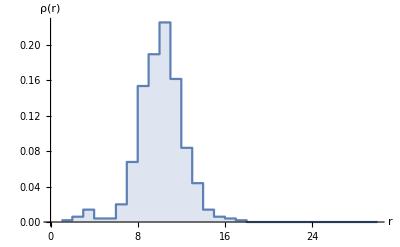

```mathematica
(* An example of a distance profile (from a random vertex) for a single random geometry *)
ListPlot[distanceProfile[generateMap["C",500],30],Joined->True,Filling->Axis,InterpolationOrder->0,AxesLabel->{"r","ρ(r)"}]
```

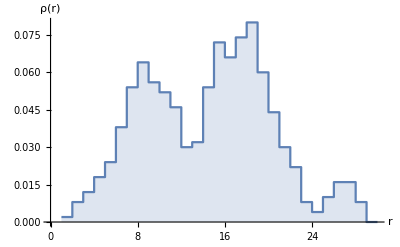

```mathematica
(* the same but for dual graph distance *)
ListPlot[dualDistanceProfile[generateMap["C",500],30],Joined->True,Filling->Axis,InterpolationOrder->0,AxesLabel->{"r","ρ(r)"}]
```

```mathematica
(* Task: Proceed to gather data for the average distance profile for different system sizes and models, and attempt finite-size scaling to extract the Hausdorff dimension *)
```

## Spectral dimension

The spectral dimension d_s of a map is related to the probability p(t) that a simple random walk on the map (or its dual) returns to its starting point after t steps: p(t) ~ t^(-d_s/2) for 1<< t << n (where n is the system size). There are various ways to measure this return probability: one can simulate a random walker and just record its returns; study a heat diffusion process; or use linear algebra as follows. The return probability ⟨p(t)⟩ averaged over all starting points of the map is related to the normalized adjacency matrix A via  ⟨p(t)⟩=Tr(A^t)/n = ∑λ_i^t/n, where λ_i are the eigenvalues of A.

```mathematica
dualAdjacencyMatrix[map_]:=Module[{dualedges,matrixentries,facedegrees},
dualedges=edgecycles[map]/.halfedgeToFaceId[map];
facedegrees=Length/@facecycles[map];
matrixentries =Tally@Join[dualedges,Reverse/@dualedges];
SparseArray[#[[1]]->#[[2]]/facedegrees[[#[[1,1]]]]&/@matrixentries]
]
```

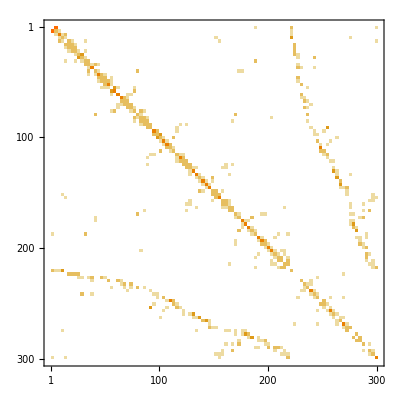

```mathematica
(* plot the adjacency matrix (for fun) *) 
MatrixPlot[dualAdjacencyMatrix[generateMap["D",300]]]
```

```mathematica
dualAdjacencySpectrum[map_]:=Sort@Eigenvalues@Normal@N@dualAdjacencyMatrix[map]
```

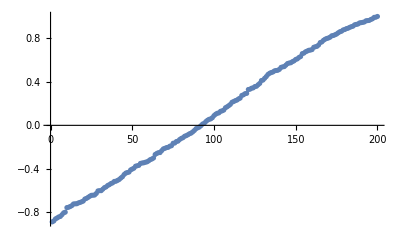

```mathematica
(* a plot of the spectrum of a random geometry *)
ListPlot[dualAdjacencySpectrum[generateMap["A",200]]]
```

```mathematica
(* The return probability of a random walker after k steps averaged over all starting points. *)
(* Notice one can may take range to be e.g. 2^Range[14] to get the return probability for {t=2,t=4,...,t=2^14} without problem. *)
returnProbability[map_,range_]:=With[{spec=dualAdjacencySpectrum[map]},Table[{t,Mean[spec^t]},{t,range}]]
```

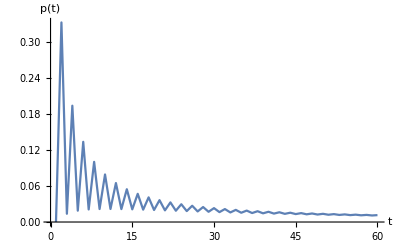

```mathematica
(* A plot of the return probability for a single random geometry *)
(* Notice the alternating pattern. Do you understand why it occurs? *)
ListPlot[returnProbability[generateMap["D",500],Range[60]],Joined->True,AxesLabel->{"t","p(t)"},PlotRange->All]
```

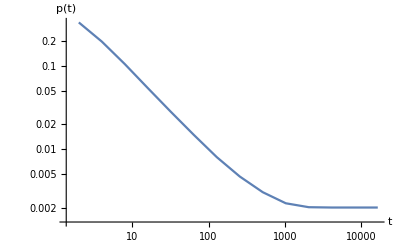

```mathematica
(* A logarithmic plot of the return probability for a single random geometry at large time, showing the finite size effects *)
(* The return probability approaches a constant at late times. What value does it take? *)
ListLogLogPlot[returnProbability[generateMap["A",500],2^Range[14]],Joined->True,AxesLabel->{"t","p(t)"}]
```

```mathematica
(* Task: Gather data for various system sizes and models and try to extract the spectral dimension by fitting the slope (in the logarithmic plot) *)
```

## Susceptibility exponent / counting exponent

Another important exponent is the susceptibility exponent γ (also known as the counting exponent) which governs the growth of the (unlabeled) partition function with increasing system size:  Z(n)~n^(γ-3)ⅇ^(-c n) (assuming we have no marking/root). One way to determine this exponent is to look for minimal necks in the map, i.e. closed paths of minimal length on the map (which for our purposes is typically length 2). For each minimal neck one may determine the distribution of the number m of faces/edges/vertices it encloses. This distribution should for large n,m be proportional to (m(n-m))^(γ-2), and fitting the data provides an estimate for γ. Be aware that for this measurement to work one needs an abundance of minimal necks, which is not necessarily the case for all models.

```mathematica
(* Below is a crude way to identify minimal necks. Do you know of a better way? *)
```

```mathematica
(* find pairs of vertices with more than one connecting edge *)
vertexPairsWithDoubleEdges[map_]:=Select[Normal@GroupBy[edgecycles[map]//Transpose[{#,#/.halfedgeToVertexId[map]}]&,Sort@Last@#&],Length[#[[2]]]>1&][[All,1]];
```

```mathematica
(* a brute force way to determine the (smallest of the two) enclosed volumes: remove the pair of vertices from the graph, and determine the sizes of the remaining connected components *)
componentSize[graph_,vertexpair_]:=Min[#,VertexCount[graph]-#]&@Length@RandomChoice@WeaklyConnectedComponents@VertexDelete[graph,vertexpair]
```

```mathematica
(* an example of the number of vertices in all the regions enclosed by minimal necks in a single random geometry *)
map=generateMap["C",200];
graph=mapGraph[map];
componentSize[mapGraph[map],#]&/@vertexPairsWithDoubleEdges[map]
```

{1,21,52,53,1,2,1,1,1,3,7,1,1,3,1,1,1,3,1,1,24,1,25,1,4,24,1,1,1,1,4,4,4,1,1,1,2,3,1,1,1,1,3,1,7,1,7,3,1,3,2,4,2,1,5,1,1,1,6,1,3,2,1,4,2,3,14,3,1,10,14,1,1,1,2,4,1,3}

```mathematica
(* Task: Produce histograms for the volume enclosed by minimal necks in random geometries of various sizes and models; make a logarithmic plot of the histogram (normalized by 1/V where V is the number of vertices of the geometry) against n(1-n/V) and extract γ from the slope of the curve. *)
```